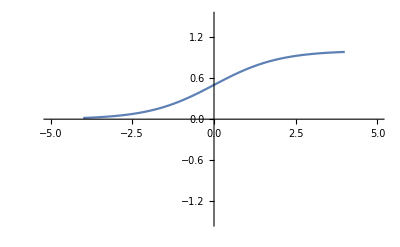

```mathematica
Plot[1/(1+Exp[-t]),{t,-4,4},PlotRange->{{-5,5},{-1.5,1.5}}]
```

```mathematica
Export["/Users/ozan/Downloads/Logistic.pdf",%60,"PDF"]
```

/Users/ozan/Downloads/Logistic.pdf

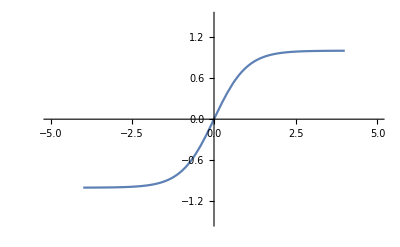

```mathematica
Plot[Tanh[t],{t,-4,4},PlotRange->{{-5,5},{-1.5,1.5}}]
```

```mathematica
Export["/Users/ozan/Downloads/Tanh.pdf",%62,"PDF"]
```

/Users/ozan/Downloads/Tanh.pdf

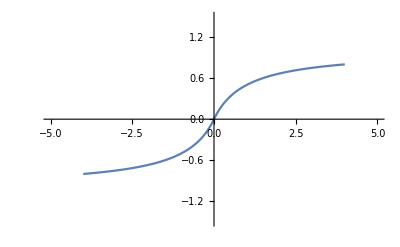

```mathematica
Plot[t/(1+Abs[t]),{t,-4,4},PlotRange->{{-5,5},{-1.5,1.5}}]
```

```mathematica
Export["/Users/ozan/Downloads/Softsign.pdf",%64,"PDF"]
```

/Users/ozan/Downloads/Softsign.pdf

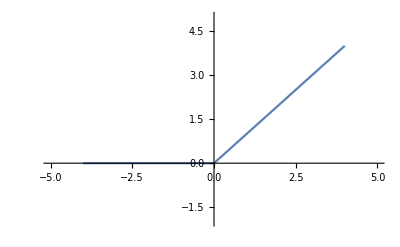

```mathematica
Plot[Piecewise[{{0,t<0},{t,t>=0}}],{t,-4,4},PlotRange->{{-5,5},{-2,5}}]
```

```mathematica
Export["/Users/ozan/Downloads/ReLU.pdf",%33,"PDF"]
```

/Users/ozan/Downloads/ReLU.pdf

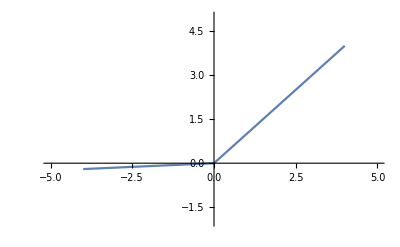

```mathematica
ϵ=0.05;
Plot[Piecewise[{{ϵ t,t<0},{t,t>=0}}],{t,-4,4},PlotRange->{{-5,5},{-2,5}}]
```

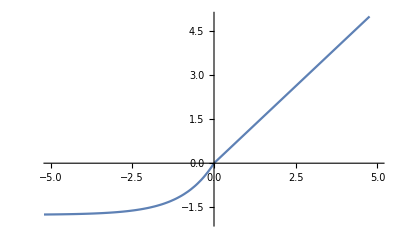

```mathematica
α=1.6732;
λ =1.0507;
Plot[Piecewise[{{λ t,t>0},{λ α (Exp[t]-1),t<=0}}],{t,-10,10},PlotRange->{{-5,5},{-2,5}}]
```

```mathematica
Export["/Users/ozan/Downloads/SELU.pdf",%68,"PDF"]
```

/Users/ozan/Downloads/SELU.pdf